## Numerators

## Algebra utilities

```mathematica
SetDirectory[NotebookDirectory[]]
<<"./tools/tensTools.m"
<<"./tools/ampTools2.1.m"
```

/Users/zeno/Desktop/LTD/program/alphaLoopMisc

The documented functions in this package are: 
 ?extractTensCoeff
 ?getSymNumericCoeff

The documented functions in this package are: 
 ?contractLorentz 
 ?contractColor 
 ?contractSpin 
 ?constructLorentzProjector 
 Make sure you have the "trace_form.log" file for the gamma-algebra

gamma traces loaded

The documented functions in this package are: 
 ?contractLorentz 
 ?contractColor 
 ?contractSpin 
 ?constructLorentzProjector 
 Make sure you have the "trace_form.log" file for the gamma-algebra

gamma traces loaded

## Numerators

### Numerator definitions

#### Double Triangle

```mathematica
dtNum[k_,l_,p1_,p2_,gs_, e_,eL_]:=(
(-I e gamma[s[11],mu,s[12]])
 I vector[k,mu1]gamma[s[12],mu1,s[13]]
(-I gs gamma[s[13],mu2,s[14]])
I vector[l,mu3]gamma[s[14],mu3,s[15]]
(-I e gamma[s[15],nu,s[16]])
I vector[l-p1-p2,mu4]gamma[s[16],mu4,s[17]]
(-I gs gamma[s[17],mu2,s[18]])
I vector[k-p1-p2,mu5]gamma[s[18],mu5,s[11]]
(-I eL gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I eL gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

dtNumerator[k_,l_,p1_,p2_]=contractSpin[dtNum[k,l,p1,p2,gs,e,eL],{k,l,p1,p2}]/.{gs->1,e->1,d->4,eL->1}
```

128 SP[k,p1] SP[k,p2] SP[l,l]-128 SP[k,l] SP[k,p2] SP[l,p1]-64 SP[k,p1] SP[k,p2] SP[l,p1]+64 SP[k,p2]^2 SP[l,p1]+64 SP[k,p2] SP[l,p1]^2-128 SP[k,l] SP[k,p1] SP[l,p2]+64 SP[k,p1]^2 SP[l,p2]-64 SP[k,p1] SP[k,p2] SP[l,p2]+128 SP[k,k] SP[l,p1] SP[l,p2]-64 SP[k,p1] SP[l,p1] SP[l,p2]-64 SP[k,p2] SP[l,p1] SP[l,p2]+64 SP[k,p1] SP[l,p2]^2+64 SP[k,l] SP[k,p2] SP[p1,p1]-64 SP[k,p2] SP[l,l] SP[p1,p1]-64 SP[k,k] SP[l,p2] SP[p1,p1]+64 SP[k,l] SP[l,p2] SP[p1,p1]+128 SP[k,p2] SP[l,p2] SP[p1,p1]+128 SP[k,l]^2 SP[p1,p2]-64 SP[k,l] SP[k,p1] SP[p1,p2]-64 SP[k,l] SP[k,p2] SP[p1,p2]-64 SP[k,k] SP[l,l] SP[p1,p2]-64 SP[k,l] SP[l,p1] SP[p1,p2]+128 SP[k,p1] SP[l,p1] SP[p1,p2]-64 SP[k,l] SP[l,p2] SP[p1,p2]+128 SP[k,p2] SP[l,p2] SP[p1,p2]-64 SP[k,l] SP[p1,p1] SP[p1,p2]+64 SP[k,l] SP[k,p1] SP[p2,p2]-64 SP[k,p1] SP[l,l] SP[p2,p2]-64 SP[k,k] SP[l,p1] SP[p2,p2]+64 SP[k,l] SP[l,p1] SP[p2,p2]+128 SP[k,p1] SP[l,p1] SP[p2,p2]-128 SP[k,l] SP[p1,p1] SP[p2,p2]-64 SP[k,l] SP[p1,p2] SP[p2,p2]

#### 2 to2 (with initial quarks)

```mathematica
twoNum[k_,l_,p_,mu_,nu_,gs_, e_,q_]:=(
(-I e gamma[s[11],nu,s[12]])
 I vector[k+q,mu1]gamma[s[12],mu1,s[13]]
(-I e gamma[s[13],mu,s[14]])
I vector[k+p,mu3]gamma[s[14],mu3,s[15]]
(-I gs gamma[s[15],mu2,s[16]])
I vector[k+l+p,mu4]gamma[s[16],mu4,s[17]]
(-I gs gamma[s[17],mu2,s[18]])
I vector[k,mu5]gamma[s[18],mu5,s[11]]
)

twoNumerator[k_,l_,p_,q_,mu_,nu_]=contractSpin[twoNum[k,l,p,mu,nu,gs,e,q],{k,l,p,q}]/.{gs->1,e->1,d->4}
```

8 g[mu,nu] SP[k,k]^2+8 g[mu,nu] SP[k,k] SP[k,l]+16 g[mu,nu] SP[k,k] SP[k,p]+8 g[mu,nu] SP[k,k] SP[k,q]+16 g[mu,nu] SP[k,l] SP[k,q]+16 g[mu,nu] SP[k,p] SP[k,q]+8 g[mu,nu] SP[k,k] SP[l,p]+8 g[mu,nu] SP[k,q] SP[l,p]-8 g[mu,nu] SP[k,k] SP[l,q]-8 g[mu,nu] SP[k,p] SP[l,q]+8 g[mu,nu] SP[k,k] SP[p,p]+8 g[mu,nu] SP[k,q] SP[p,p]+8 g[mu,nu] SP[k,l] SP[p,q]-16 SP[k,k] vector[k,mu] vector[k,nu]-32 SP[k,l] vector[k,mu] vector[k,nu]-32 SP[k,p] vector[k,mu] vector[k,nu]-16 SP[l,p] vector[k,mu] vector[k,nu]-16 SP[p,p] vector[k,mu] vector[k,nu]+8 SP[k,k] vector[k,nu] vector[l,mu]+16 SP[k,p] vector[k,nu] vector[l,mu]+8 SP[p,q] vector[k,nu] vector[l,mu]+8 SP[k,k] vector[k,mu] vector[l,nu]-8 SP[p,q] vector[k,mu] vector[l,nu]-16 SP[k,l] vector[k,nu] vector[p,mu]-8 SP[l,q] vector[k,nu] vector[p,mu]+8 SP[k,k] vector[l,nu] vector[p,mu]+8 SP[k,q] vector[l,nu] vector[p,mu]+8 SP[l,q] vector[k,mu] vector[p,nu]-8 SP[k,k] vector[l,mu] vector[p,nu]-8 SP[k,q] vector[l,mu] vector[p,nu]-8 SP[k,k] vector[k,nu] vector[q,mu]-16 SP[k,l] vector[k,nu] vector[q,mu]-16 SP[k,p] vector[k,nu] vector[q,mu]-8 SP[l,p] vector[k,nu] vector[q,mu]-8 SP[p,p] vector[k,nu] vector[q,mu]+8 SP[k,k] vector[l,nu] vector[q,mu]+8 SP[k,p] vector[l,nu] vector[q,mu]-8 SP[k,l] vector[p,nu] vector[q,mu]-8 SP[k,k] vector[k,mu] vector[q,nu]-16 SP[k,l] vector[k,mu] vector[q,nu]-16 SP[k,p] vector[k,mu] vector[q,nu]-8 SP[l,p] vector[k,mu] vector[q,nu]-8 SP[p,p] vector[k,mu] vector[q,nu]+8 SP[k,k] vector[l,mu] vector[q,nu]+8 SP[k,p] vector[l,mu] vector[q,nu]-8 SP[k,l] vector[p,mu] vector[q,nu]

#### Bubble

```mathematica
bubNum[k_,l_,p_,mu_,nu_,gs_, e_,q_]:=(
(-I e gamma[s[11],nu,s[12]])
 I vector[k-q,mu1]gamma[s[12],mu1,s[13]]
(-I e gamma[s[13],mu,s[14]])
I vector[k,mu3]gamma[s[14],mu3,s[15]]
(-I gs gamma[s[15],mu2,s[16]])
I vector[l,mu4]gamma[s[16],mu4,s[17]]
(-I gs gamma[s[17],mu2,s[18]])
I vector[k,mu5]gamma[s[18],mu5,s[11]]
)

bubNumerator[k_,l_,p_,q_,mu_,nu_]=contractSpin[bubNum[k,l,p,mu,nu,gs,e,q],{k,l,p,q}]/.{gs->1,e->1,d->4}
```

8 g[mu,nu] SP[k,k] SP[k,l]-16 g[mu,nu] SP[k,l] SP[k,q]+8 g[mu,nu] SP[k,k] SP[l,q]-32 SP[k,l] vector[k,mu] vector[k,nu]+8 SP[k,k] vector[k,nu] vector[l,mu]+8 SP[k,k] vector[k,mu] vector[l,nu]+16 SP[k,l] vector[k,nu] vector[q,mu]-8 SP[k,k] vector[l,nu] vector[q,mu]+16 SP[k,l] vector[k,mu] vector[q,nu]-8 SP[k,k] vector[l,mu] vector[q,nu]

#### 2 to 2 (with one initial gluon and one initial quark)

```mathematica
twoV2Num[k_,l_,mu_,nu_,gs_, e_,q_]:=(
(-I e gamma[s[11],mu,s[12]])
 I vector[k+q,mu1]gamma[s[12],mu1,s[13]]
(-I gs gamma[s[13],mu2,s[14]])
I vector[l,mu3]gamma[s[14],mu3,s[15]]
(-I e gamma[s[15],nu,s[16]])
I vector[l+q,mu4]gamma[s[16],mu4,s[17]]
(-I gs gamma[s[17],mu2,s[18]])
I vector[k,mu5]gamma[s[18],mu5,s[11]]
)

twoV2Numerator[k_,l_,q_,mu_,nu_]=contractSpin[twoV2Num[k,l,mu,nu,gs,e,q],{k,l,q}]/.{gs->1,e->1,d->4}
```

-8 g[mu,nu] SP[k,k] SP[l,l]-8 g[mu,nu] SP[k,q] SP[l,l]-8 g[mu,nu] SP[k,k] SP[l,q]-8 g[mu,nu] SP[k,l] SP[q,q]+16 SP[l,l] vector[k,mu] vector[k,nu]+16 SP[l,q] vector[k,mu] vector[k,nu]+8 SP[q,q] vector[k,nu] vector[l,mu]-32 SP[k,l] vector[k,mu] vector[l,nu]-16 SP[k,q] vector[k,mu] vector[l,nu]-16 SP[l,q] vector[k,mu] vector[l,nu]-8 SP[q,q] vector[k,mu] vector[l,nu]+16 SP[k,k] vector[l,mu] vector[l,nu]+16 SP[k,q] vector[l,mu] vector[l,nu]+8 SP[l,l] vector[k,nu] vector[q,mu]+8 SP[k,k] vector[l,nu] vector[q,mu]-16 SP[k,l] vector[l,nu] vector[q,mu]-16 SP[k,l] vector[k,mu] vector[q,nu]+8 SP[l,l] vector[k,mu] vector[q,nu]+8 SP[k,k] vector[l,mu] vector[q,nu]

#### 2 to2 s - channel

```mathematica
sChannelBubNum[k_,l_,mu_,nu_,gs_, e_,q_]:=(
(-I e gamma[s[11],nu,s[12]])
 I vector[k,mu1]gamma[s[12],mu1,s[13]]
(-I e gamma[s[13],mu,s[14]])
I vector[k+q,mu3]gamma[s[14],mu3,s[15]]
(-I gs gamma[s[15],mu2,s[16]])
I vector[k+q-l,mu4]gamma[s[16],mu4,s[17]]
(-I gs gamma[s[17],mu2,s[18]])
I vector[k+q,mu5]gamma[s[18],mu5,s[11]]
)

sChannelBubNumerator[k_,l_,q_,mu_,nu_]=contractSpin[sChannelBubNum[k,l,mu,nu,gs,e,q],{k,l,q}]/.{gs->1,e->1,d->4}
```

8 g[mu,nu] SP[k,k]^2-8 g[mu,nu] SP[k,k] SP[k,l]+24 g[mu,nu] SP[k,k] SP[k,q]+16 g[mu,nu] SP[k,q]^2-16 g[mu,nu] SP[k,k] SP[l,q]-16 g[mu,nu] SP[k,q] SP[l,q]+8 g[mu,nu] SP[k,k] SP[q,q]+8 g[mu,nu] SP[k,l] SP[q,q]+8 g[mu,nu] SP[k,q] SP[q,q]-16 SP[k,k] vector[k,mu] vector[k,nu]+32 SP[k,l] vector[k,mu] vector[k,nu]-32 SP[k,q] vector[k,mu] vector[k,nu]+32 SP[l,q] vector[k,mu] vector[k,nu]-16 SP[q,q] vector[k,mu] vector[k,nu]-8 SP[k,k] vector[k,nu] vector[l,mu]-16 SP[k,q] vector[k,nu] vector[l,mu]-8 SP[q,q] vector[k,nu] vector[l,mu]-8 SP[k,k] vector[k,mu] vector[l,nu]-16 SP[k,q] vector[k,mu] vector[l,nu]-8 SP[q,q] vector[k,mu] vector[l,nu]-8 SP[k,k] vector[k,nu] vector[q,mu]+16 SP[k,l] vector[k,nu] vector[q,mu]-16 SP[k,q] vector[k,nu] vector[q,mu]+16 SP[l,q] vector[k,nu] vector[q,mu]-8 SP[q,q] vector[k,nu] vector[q,mu]-8 SP[k,k] vector[k,mu] vector[q,nu]+16 SP[k,l] vector[k,mu] vector[q,nu]-16 SP[k,q] vector[k,mu] vector[q,nu]+16 SP[l,q] vector[k,mu] vector[q,nu]-8 SP[q,q] vector[k,mu] vector[q,nu]

#### 2 to 2 u - channel

```mathematica
uChannelNum[k_,l_,mu_,nu_,gs_, e_,q_]:=(
(-I e gamma[s[11],mu,s[12]])
 I vector[k+q,mu1]gamma[s[12],mu1,s[13]]
(-I gs gamma[s[13],mu2,s[14]])
I vector[k+l+q,mu3]gamma[s[14],mu3,s[15]]
(-I e gamma[s[15],nu,s[16]])
I vector[k+l,mu4]gamma[s[16],mu4,s[17]]
(-I gs gamma[s[17],mu2,s[18]])
I vector[k,mu5]gamma[s[18],mu5,s[11]]
)

uChannelNumerator[k_,l_,q_,mu_,nu_]=contractSpin[uChannelNum[k,l,mu,nu,gs,e,q],{k,l,q}]/.{gs->1,e->1,d->4}
```

-8 g[mu,nu] SP[k,k]^2-16 g[mu,nu] SP[k,k] SP[k,l]-16 g[mu,nu] SP[k,k] SP[k,q]-16 g[mu,nu] SP[k,l] SP[k,q]-16 g[mu,nu] SP[k,q]^2-8 g[mu,nu] SP[k,k] SP[l,l]-8 g[mu,nu] SP[k,q] SP[l,l]-8 g[mu,nu] SP[k,k] SP[l,q]-16 g[mu,nu] SP[k,q] SP[l,q]+8 g[mu,nu] SP[k,k] SP[q,q]+8 g[mu,nu] SP[k,l] SP[q,q]+16 SP[l,l] vector[k,mu] vector[k,nu]-16 SP[q,q] vector[k,mu] vector[k,nu]+16 SP[k,k] vector[k,nu] vector[l,mu]+16 SP[k,q] vector[k,nu] vector[l,mu]-8 SP[q,q] vector[k,nu] vector[l,mu]-16 SP[k,k] vector[k,mu] vector[l,nu]-32 SP[k,l] vector[k,mu] vector[l,nu]-16 SP[k,q] vector[k,mu] vector[l,nu]-16 SP[l,q] vector[k,mu] vector[l,nu]-8 SP[q,q] vector[k,mu] vector[l,nu]+16 SP[k,k] vector[l,mu] vector[l,nu]+16 SP[k,q] vector[l,mu] vector[l,nu]+16 SP[k,q] vector[k,nu] vector[q,mu]+8 SP[l,l] vector[k,nu] vector[q,mu]+16 SP[l,q] vector[k,nu] vector[q,mu]-8 SP[k,k] vector[l,nu] vector[q,mu]-16 SP[k,l] vector[l,nu] vector[q,mu]+16 SP[k,q] vector[k,mu] vector[q,nu]+8 SP[l,l] vector[k,mu] vector[q,nu]+8 SP[k,k] vector[l,mu] vector[q,nu]+16 SP[k,q] vector[l,mu] vector[q,nu]-16 SP[k,k] vector[q,mu] vector[q,nu]-16 SP[k,l] vector[q,mu] vector[q,nu]

### Scalar product, norm, tensor definitions

```mathematica
SP[k_,q_]:=k[[1]]q[[1]]-k[[2]]q[[2]]-k[[3]]q[[3]]-k[[4]]q[[4]]
norm[k_]:=Sqrt[k[[2]]^2+k[[3]]^2+k[[4]]^2]
vector[k_,mu_]:=k[[mu]]
g[mu_,nu_]:=-KroneckerDelta[mu,nu]+2 KroneckerDelta[mu,0]KroneckerDelta[nu,0]
```

### Tests

#### Double triangle, u - channel and st - channel equivalences

Numerators of cut diagrams obtained from the same vacuum bubble are the same up to re-routing

```mathematica
Simplify[dtNumerator[{k0,kx,ky,kz},-{l0,lx,ly,lz}-{q0,qx,qy,qz},-{q0,qx,qy,qz},1,1]-twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},1,1]]
```

0

```mathematica
Simplify[dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},1,1]-uChannelNumerator[{k0,kx,ky,kz}-{q0,qx,qy,qz},{l0,lx,ly,lz}-{k0,kx,ky,kz},{q0,qx,qy,qz},1,1]]
```

0

#### Bubble correction, s - channel and t - channel equivalences

Numerators of cut diagrams obtained from the same vacuum bubble are the same up to re - routing

```mathematica
Simplify[bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},1,1]-sChannelBubNumerator[{k0,kx,ky,kz}-{q0,qx,qy,qz},-{l0,lx,ly,lz}+{k0,kx,ky,kz},{q0,qx,qy,qz},1,1]]
```

0

```mathematica
Simplify[bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},1,1]-twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz}-{k0,kx,ky,kz},{0,0,0,0},-{q0,qx,qy,qz},1,1]]
```

0

## Integrands

## -Graphics-

### Supergraph

```mathematica
dtSupergraph[k_,l_,p1_,p2_]:=(dtNumerator[k,l,p1,p2]/(SP[k,k]SP[l,l]SP[k-l,k-l]SP[l-p1-p2,l-p1-p2]SP[k-p1-p2,k-p1-p2]))

dtSupergraph[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}];
```

### Causal flow

```mathematica
phi[t_,k_,l_]:={t k, t l};

jacPhi[t_,k_,l_]:=t^6;
```

#### Flow solutions

```mathematica
vLsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,lx,ly,lz}]+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]);
vRsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]);
rLsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,lx,ly,lz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]);
rRsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}]+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]);
```

#### Dirac delta jacobians

```mathematica
vLdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,ax,ay,az}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{ax,ay,az}] ,{ax,ay,az}])/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
vRdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{sx,sy,sz}] ,{sx,sy,sz}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
rLdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}-{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
rRdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,ax,ay,az}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}-{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};

vLdiracJ[1,2,3,4,5,7,2,2,3,4,5,6,7,8];
```

### Virtual contributions

#### Virtual left

```mathematica
dtVirtualLeft[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2k0]SP[{k0,kx,ky,kz}-{l0,lx,ly,lz},{k0,kx,ky,kz}-{l0,lx,ly,lz}]SP[{k0-p10-p20,kx-p1x-p2x,ky-p1y-p2y,kz-p1z-p2z},{k0-p10-p20,kx-p1x-p2x,ky-p1y-p2y,kz-p1z-p2z}]))/.{p20->-p10+l0+norm[{0,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2(k0-l0)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]))/.{k0->l0+norm[{0,kx-lx,ky-ly,kz-lz}]}/.{p20->-p10+l0+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2(k0-p10-p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0-l0,kx-lx,ky-ly,kz-lz},{k0-l0,kx-lx,ky-ly,kz-lz}]))/.{k0->p10+p20+norm[{0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{p20->-p10+l0+norm[{0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]})

dtVirtualLeft[1,2.3,3,4,3,5,6,7,8,9,1,2,6]
```

-10.1235

#### Virtual Right

```mathematica
dtVirtualRight[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2l0]SP[{k0,kx,ky,kz}-{l0,lx,ly,lz},{k0,kx,ky,kz}-{l0,lx,ly,lz}]SP[{l0-p10-p20,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z},{l0-p10-p20,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z}]))/.{p20->-p10+k0+norm[{0,kx,kx,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2(k0-l0)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]))/.{p20->-p10+k0+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{l0->k0+norm[{0,kx-lx,ky-ly,kz-lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2(l0-p10-p20)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{k0-l0,kx-lx,ky-ly,kz-lz},{k0-l0,kx-lx,ky-ly,kz-lz}]))/.{l0->p10+p20+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{p20->-p10+k0+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]})

dtVirtualRight[1,2.3,3,4,3,5,6,7,8,9,1,2,6]
```

-4.12873

### Real contributions

#### Real right

```mathematica
dtRealLeft[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=(dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(l0-k0)2(l0-p10-p20)]SP[{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{p20->-p10+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+l0}/.{l0->k0+norm[{0,lx-kx,ly-kx,lz-kz}]}/.{k0->norm[{0,kx,ky,kz}]}
```

```mathematica
dtRealLeft[1,2.3,3,4,3,5,6,7,8,9,1,2,6]
```

0.544478

#### Real left

```mathematica
dtRealRight[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=(dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(-l0+k0)2(k0-p10-p20)]SP[{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]))/.{p20->-p10+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+k0}/.{k0->l0+norm[{0,lx-kx,ly-kx,lz-kz}]}/.{l0->norm[{0,lx,ly,lz}]}
```

```mathematica
dtRealRight[1,2.3,3,4,3,5,6,7,8,9,1,2,6]
```

-0.00931383

### Cross - section per supergraph

#### Toy model

```mathematica
dtSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=dtVirtualLeft[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+dtVirtualRight[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+dtRealLeft[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+dtRealRight[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]
```

```mathematica
dtSum[1,2.3,3,4,3,5,6,7,8,9,1,2,6]
```

-13.7171

#### LU

```mathematica
dtLUrep[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,q0_,mu_,nu_]:=Module[{},
vLt=vLsol[kx,ky,kz,lx,ly,lz,qx,qy,qz,q0];
vRt=vRsol[kx,ky,kz,lx,ly,lz,qx,qy,qz,q0];
rLt=rLsol[kx,ky,kz,lx,ly,lz,qx,qy,qz,q0];
rRt=rRsol[kx,ky,kz,lx,ly,lz,qx,qy,qz,q0];

sum=


];
```

### IR limits

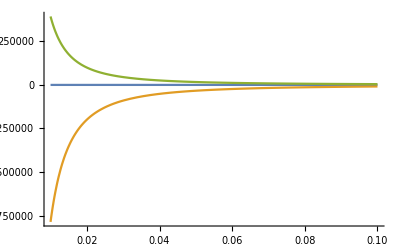

```mathematica
Plot[{dtSum[1,1,1,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1], dtVirtualRight[1,1,1,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1], dtRealRight[1,1,1,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1]},{eps,0.01,0.1},PlotRange->All]
```

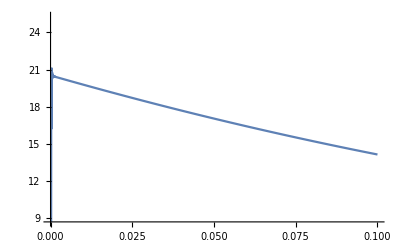

```mathematica
Plot[{dtSum[0.3,0.3,0.3,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1]},{eps,0.0,0.1}]
```

### Back-to-backness

30.3273

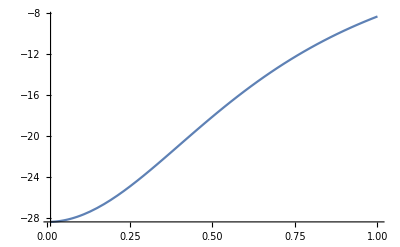

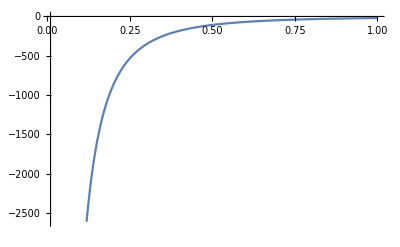

```mathematica
dtSumBTB[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=(*dtVirtualLeft[kx,ky,kz,0,0,norm[{0,lx,ly,lz}],qx,qy,qz,mu,nu]+*)dtVirtualRight[0,0,norm[{0,kx,ky,kz}],lx,ly,lz,qx,qy,qz,mu,nu]+dtRealRight[0,0,norm[{0,kx,ky,kz}],lx,ly,lz,qx,qy,qz,mu,nu](*dtRealLeft[0,0,norm[{0,kx,ky,kz}],lx,ly,lz,qx,qy,qz,mu,nu]+dtRealRight[kx,ky,kz,0,0,norm[{0,lx,ly,lz}],qx,qy,qz,mu,nu]+
dtRealLeft[kx,ky,kz,qx,qy,qz+norm[{0,lx,ly,lz}],qx,qy,qz,mu,nu]+dtRealRight[qx,qy,qz+norm[{0,kx,ky,kz}],lx,ly,lz,qx,qy,qz,mu,nu]*)

dtSumBTB[0.,0.3,1,0.,1,0.5,0.,0.,0.,1,1 ]

Plot[dtSumBTB[0.,0.+eps,1,0.,0.5,0.5,0.,0.,0.,1,1 ],{eps,0.01,1}]

Plot[dtVirtualRight[0.,0.+eps,1,0.,0.,Sqrt[0.5],0.,0.,0.,1,1],{eps,0.01,1}]
```

## -Graphics-

### Usual Cut

```mathematica
usualCut[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},mu,nu]/(Abs[2 l0 2 (k0+q0) 2(l0+k0)] SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]^2))/.{q0->-k0-norm[{k0,kx,ky,kz}+{q0,qx,qy,qz}]}/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}] })
```

```mathematica
usualCut[kx,ky,kz,lx,ly,lz,0,0,0,1,1];
```

### Weird Cut 1

This is the true and unique ISR singularity

-Graphics-

```mathematica
weirdCut1[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=-((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},mu,nu]/(Abs[2l0 2(k0+q0) 4(k0)^3 ]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]))/.{q0->-k0-norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((1/Abs[2l0 2(k0+q0) 4(k0)^2])D[twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p0,0,0,0},{q0,qx,qy,qz},mu,nu]/(SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p0,0,0,0},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p0,0,0,0}]),p0])/.{q0->-k0-norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]}/.{p0->0}
```

### Weird Cut 2

This one is a diagram without support, and should not be included ultimately.Indeed, there is no such singularity in the original diagram (once energy conservation is applied)

```mathematica
weirdCut2[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},mu,nu]/(Abs[2(k0+l0) 2(k0+q0) 4(k0)^3 ]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{q0->-k0-norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{l0->-k0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}]}/.{k0->-norm[{0,kx,ky,kz}]})-
(((1/Abs[2norm[{0,kx,ky,kz}+{0,lx,ly,lz}] 2(k0+q0) 4(k0)^2])D[twoNumerator[{k0,kx,ky,kz},{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz},{p0,0,0,0},{q0,qx,qy,qz},mu,nu]/(SP[{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz},{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz}]),p0])/.{q0->-k0-norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{k0->-norm[{0,kx,ky,kz}]}/.{p0->0})
```

### Cross section per supergraph

```mathematica
twoSum[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=usualCut[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]+weirdCut1[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]+weirdCut2weirdCut1[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]
```

### Ir limits

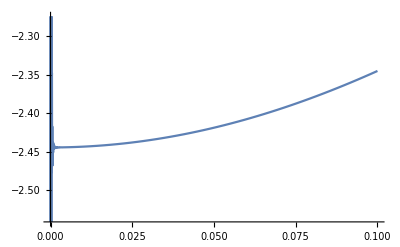

```mathematica
Plot[{weirdCut1[0,eps,0.5,0,0,1,0,0,0,1,1]+usualCut[0,eps,0.5,0,0,1,0,0,0,1,1]},{eps,0,0.1}]
```

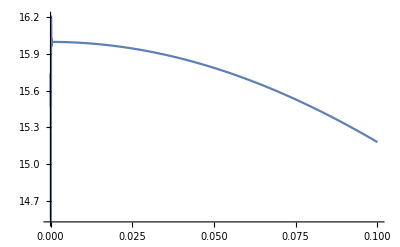

```mathematica
Plot[{weirdCut2[0,eps,-0.5,0,0,1,0,0,0,1,1]+usualCut[0,eps,-0.5,0,0,1,0,0,0,1,1]},{eps,0,0.1}]
```

## -Graphics-

### Usual cut

```mathematica
uChannelUsualCut[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},mu,nu]/(Abs[2 l0 2 (k0+l0)2(k0+q0)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{q0,qx,qy,qz},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{q0,qx,qy,qz}]))/.{q0->-k0-norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})

uChannelUsualCut[kx,ky,kz,lx,ly,lz,qx,qy,qz,1,1];
```

### Weird cut 1

```mathematica
uChannelWeirdCut1[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},mu,nu]/(Abs[2l0 2k0 2(k0+q0)]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{q0,qx,qy,qz},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{q0,qx,qy,qz}]))/.{q0->-k0-norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})

uChannelWeirdCut1[kx,ky,kz,lx,ly,lz,qx,qy,qz,1,1];
```

### Weird Cut 2

```mathematica
uChannelWeirdCut2[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},mu,nu]/(Abs[2 l0 2 (k0+l0)2(k0+l0+q0)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}+{q0,qx,qy,qz},{k0,kx,ky,kz}+{q0,qx,qy,qz}]))/.{q0->-l0-k0-norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,qx,qy,qz}]}/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})

uChannelWeirdCut2[kx,ky,kz,lx,ly,lz,qx,qy,qz,1,1];
```

### Cross section per supergraph

```mathematica
uChannelSum[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=uChannelUsualCut[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]+uChannelWeirdCut1[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]+uChannelWeirdCut2[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]
```

### Ir limits

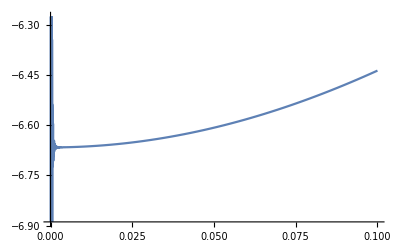

```mathematica
Plot[{uChannelWeirdCut1[0,eps,0.5,0,0,0.3,0,0,0,1,1]+uChannelUsualCut[0,eps,0.5,0,0,0.3,0,0,0,1,1]},{eps,0,0.1}]
```

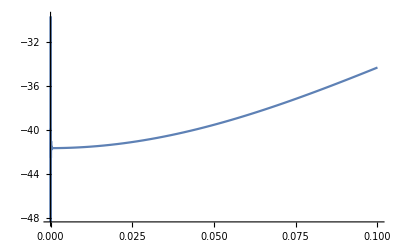

```mathematica
Plot[{uChannelWeirdCut2[0,eps,0.5,0,0,-0.3,0,0,0,1,1]+uChannelUsualCut[0,eps,0.5,0,0,-0.3,0,0,0,1,1]},{eps,0,0.1}]
```

## -Graphics-

### Only cut

This diagram has no singularities

```mathematica
sChannelBub[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((sChannelBubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},mu,nu]/(Abs[2l0 2 (k0+q0-l0)2 k0] SP[{k0,kx,ky,kz}+{q0,qx,qy,qz},{k0,kx,ky,kz}+{q0,qx,qy,qz}]^2))/.{q0->l0-k0+norm[{0,kx,ky,kz}+{0,qx,qy,qz}-{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})

sChannelBub[kx,ky,kz,lx,ly,lz,0,0,0,1,1];
```

### Cross section per supergraph

```mathematica
sChannelSum[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=sChannelBub[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]
```

## -Graphics-

### Real cut

```mathematica
bdReal[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},mu,nu]/(Abs[2 l0 2 (k0-l0)2(k0-q0)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]^2))/.{q0->k0+norm[{0,kx,ky,kz}-{0,qx,qy,qz}]}/.{k0->l0+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})
```

### Virtual cut

```mathematica
bdVirtual[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=(D[((bubNumerator[{k0,kx,ky,kz},{norm[{0,lx,ly,lz}],lx,ly,lz},{p0,0,0,0},{q0,qx,qy,qz},mu,nu]/(Abs[(2 k0)^2 2(k0-q0)2norm[{0,lx,ly,lz}]]SP[{k0,kx,ky,kz}+{p0,0,0,0}-{norm[{0,lx,ly,lz}],lx,ly,lz},{k0,kx,ky,kz}+{p0,0,0,0}-{norm[{0,lx,ly,lz}],lx,ly,lz}]))+(bubNumerator[{k0,kx,ky,kz},{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz},{p0,0,0,0},{q0,qx,qy,qz},mu,nu]/(Abs[(2 k0)^2 2(k0-q0)2 norm[{0,lx,ly,lz}-{0,kx,ky,kz}]]SP[{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz},{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz}]))),p0]/.{p0->0}/.{q0->k0+norm[{0,kx,ky,kz}-{0,qx,qy,qz}]}/.{k0->norm[{0,kx,ky,kz}]})
bdVirtual[kx,ky,kz,lx,ly,lz,qx,qy,qz,1,1];
```

### Cross section per supergraph

```mathematica
bubbleSum[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=bdReal[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]+bdVirtual[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu];
```

### Ir limits

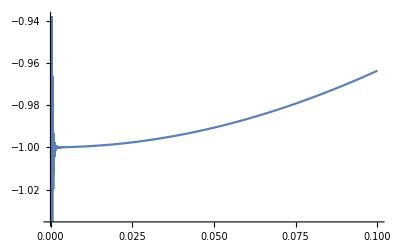

```mathematica
Plot[{bubbleSum[0,eps,1,0,0,0.5,0,0,0,1,1](*,bdVirtual[0,eps,1,0,0,0.5,0,0,0,1,1], bdReal[0,eps,1,0,0,0.5,0,0,0,1,1]*)},{eps,0,0.1}]
```

## -Graphics-

### Usual cut

```mathematica
v2UsualCut[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},mu,nu]/(Abs[2k0 2(k0+l0+q0)2l0]SP[{k0,kx,ky,kz}+{q0,qx,qy,qz},{k0,kx,ky,kz}+{q0,qx,qy,qz}]SP[{l0,lx,ly,lz}+{q0,qx,qy,qz},{l0,lx,ly,lz}+{q0,qx,qy,qz}]))/.{q0->-k0-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,qx,qy,qz}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->-norm[{0,kx,ky,kz}]})

v2UsualCut[kx,ky,kz,lx,ly,lz,0,0,0,1,1];
```

### Weird cut 1

This one is a diagram without support, and should not be included ultimately. Indeed, there is no such singularity in the original diagram (once energy conservation is applied)

```mathematica
v2WeirdCut1[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},mu,nu]/(Abs[2k0 2(k0+q0)2(k0+l0+q0)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{l0,lx,ly,lz}+{q0,qx,qy,qz},{l0,lx,ly,lz}+{q0,qx,qy,qz}]))/.{l0->-k0-q0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,qx,qy,qz}]}/.{q0->-k0-norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{k0->-norm[{0,kx,ky,kz}]})

v2WeirdCut1[kx,ky,kz,lx,ly,lz,0,0,0,1,1];
```

### Weird cut 2

This is the true and unique ISR singularity

```mathematica
v2WeirdCut2[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},mu,nu]/(Abs[2 l0 2 (k0+q0) 2 k0]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{q0,qx,qy,qz},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{q0,qx,qy,qz}] SP[{l0,lx,ly,lz}+{q0,qx,qy,qz},{l0,lx,ly,lz}+{q0,qx,qy,qz}]))/.{q0->-k0+norm[{0,kx,ky,kz}+{0,qx,qy,qz}]}/.{k0->-norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})

v2WeirdCut2[kx,ky,kz,lx,ly,lz,0,0,0,1,1];
```

### Cross section per supergraph

```mathematica
stChannelSum[kx_,ky_,kz_,lx_,ly_,lz_,qx_,qy_,qz_,mu_,nu_]:=v2UsualCut[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]+v2WeirdCut1[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]+v2WeirdCut2[kx,ky,kz,lx,ly,lz,qx,qy,qz,mu,nu]
```

### Ir limits

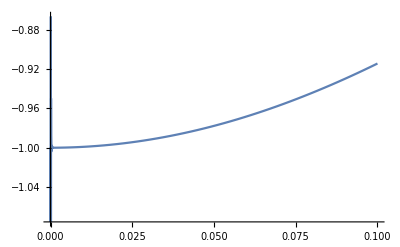

```mathematica
Plot[{v2UsualCut[0,eps,-0.5,0,0,1,0,0,0,1,1]+v2WeirdCut1[0,eps,-0.5,0,0,1,0,0,0,1,1](*, bdReal[0,eps,1,0,0,0.5,0,0,0,1,1]*)},{eps,0,0.1}]
```

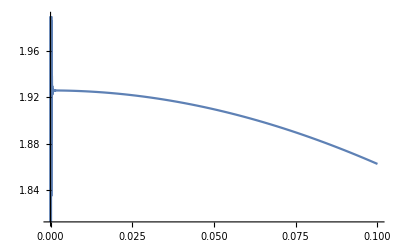

```mathematica
Plot[{v2UsualCut[0,eps,0.5,0,0,1,0,0,0,1,1]+v2WeirdCut2[0,eps,0.5,0,0,1,0,0,0,1,1](*, bdReal[0,eps,1,0,0,0.5,0,0,0,1,1]*)},{eps,0,0.1}]
```